## 17 WP groups

```mathematica
Clear["Global`*"]
Needs["Wpgroups`"]
quotientsize={3,3};
a={2,0};
(*define lattice vector b depending on lattice type*)
boblique={1/3,1}*a[[1]];
brectang={0,1/2}*a[[1]];
bcrectang={1/2,1}*a[[1]];
bsquare={0,1}*a[[1]];
bhexa={1/2,Sqrt[3]/2}*a[[1]];
brule={"oblique"->boblique,"rectang" ->brectang,"crectang" ->bcrectang,"square" -> bsquare,"hexa" -> bhexa};
names={p1,p2,pm,pg,cm,pmm,pmg,pgg,cmm,p4,p4m,p4g,p3,p3m1,p31m,p6,p6m};
dogroup=(Print[#];Show @@quotientgrafics@@{quotientsize[[1]],quotientsize[[2]],creategroup[a,(wplattice[#])/.brule,#]})&;
```

p1

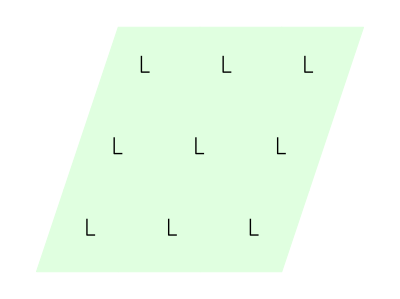

p2

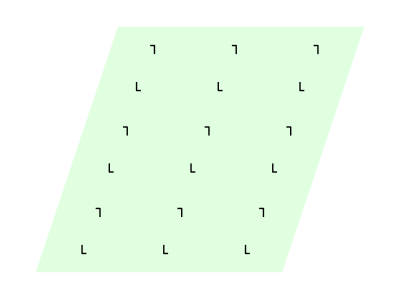

pm

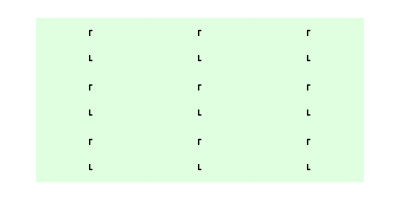

pg

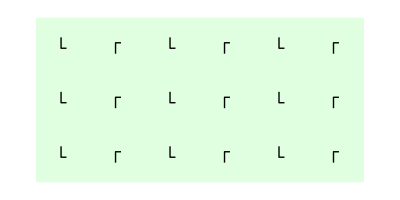

cm

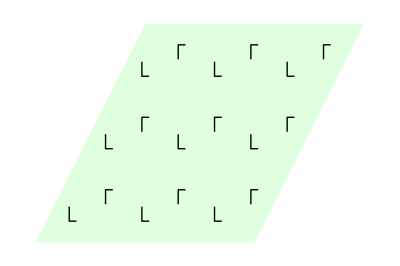

pmm

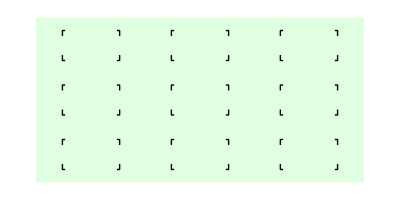

pmg

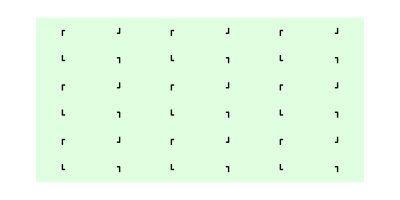

pgg

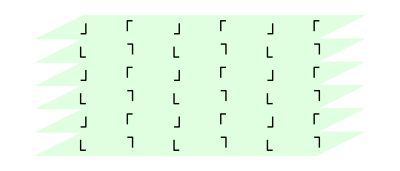

cmm

$Aborted

p4

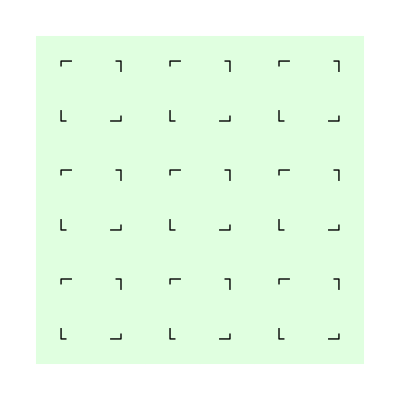

p4m

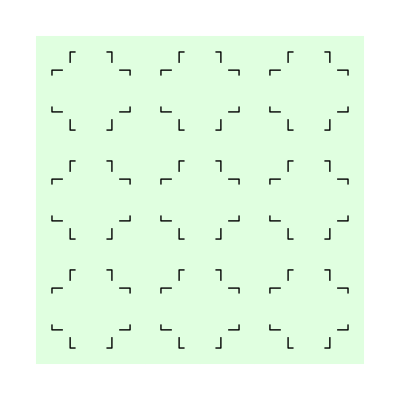

p4g

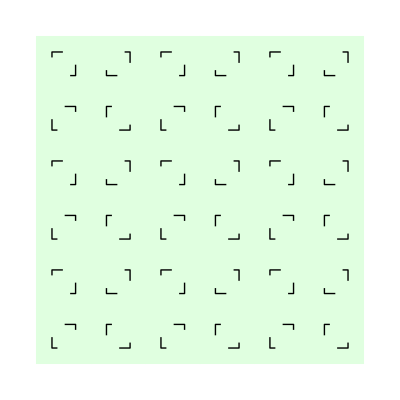

p3

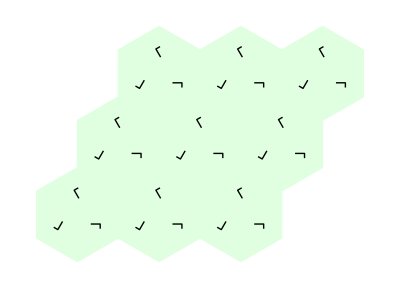

p3m1

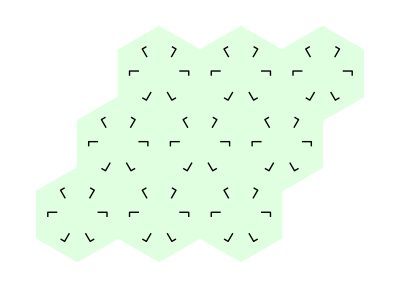

p31m

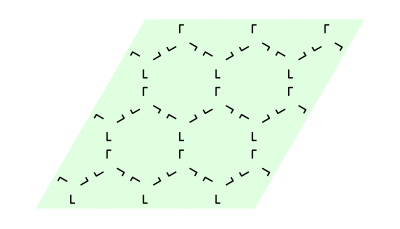

p6

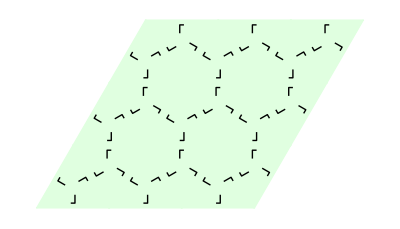

p6m

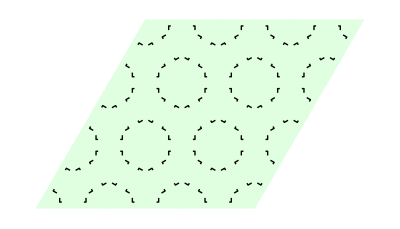

```mathematica
(*quotientpattern[quotientsize[[1]],quotientsize[[2]],creategroup[a,(name/.wplattice)/.brule,name]]*)
(*Do[n=names[[i]];Print[n];Show @@quotientgrafics@@{quotientsize[[1]],quotientsize[[2]],creategroup[a,(n/.wplattice)/.brule,n]},
{i,Length[names]}]*)
(*(Print[#];Show @@quotientgrafics@@{quotientsize[[1]],quotientsize[[2]],creategroup[a,(#/.wplattice)/.brule,#]}) &/@{p31m,p6m}*)
dogroup["p1"]
dogroup["p2"]
dogroup["pm"]
dogroup["pg"]
dogroup["cm"]
dogroup["pmm"]
dogroup["pmg"]
dogroup["pgg"]
dogroup["cmm"]
dogroup["p4"]
dogroup["p4m"]
dogroup["p4g"]
dogroup["p3"]
dogroup["p3m1"]
dogroup["p31m"]
dogroup["p6"]
dogroup["p6m"]
```

## snub-square

2

4

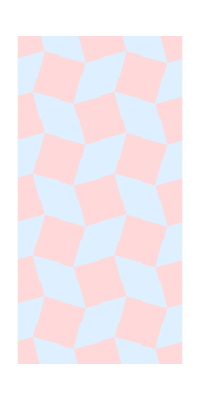

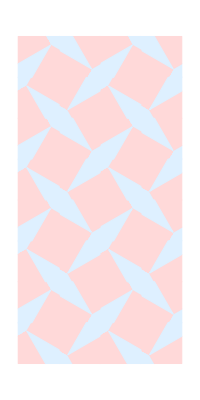

{{{0,1/2},{1/2+1/4 (1-√3)+1/4 (-3+√3)+1/4 (-1+√3),1/2+1/4 (1-√3)+1/4 (3-√3)+1/4 (-3+√3)},{0,2-√3}},{{1/2+1/4 (1-√3)+1/4 (-3+√3)+1/4 (-1+√3),1/2+1/4 (1-√3)+1/4 (3-√3)+1/4 (-3+√3)},{2-√3,0},{0,0},{0,2-√3}},{{1/2+1/4 (1-√3)+1/4 (-3+√3)+1/4 (-1+√3),1/2+1/4 (1-√3)+1/4 (3-√3)+1/4 (-3+√3)},{2-√3,0},{1/2,0}}}

9

False

```mathematica
Needs["Patterns`"]
Needs["Wpgroups`"]
Needs["Settings`"]
nrepx=2
nrepy=4
Show @@ quotientgrafics[nrepx,nrepy,creategroup[a,(wplattice[#])/.brule,#],formssnub[],graficsnubface]&["p4g"]
Show @@ quotientgrafics[nrepx,nrepy,creategroup[a,(wplattice[#])/.brule,#],formssnub[Pi/12],graficsnubface]&["p4g"]
```

4

4

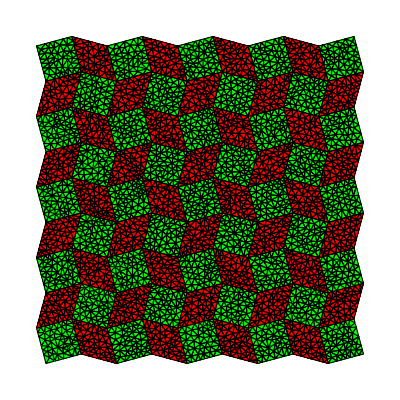

```mathematica
Needs["Settings`"]
Needs["Patterns`"]
Needs["Wpgroups`"]
Needs["NDSolve`FEM`"]
nrepx=4;
nrepy=4;
p=quotientmeshgen[nrepx,nrepy,creategroup[a,(wplattice[#])/.brule,#],meshgensoutersnub[],{"MaxCellMeasure"->0.02}]&["p4g"];
p["Wireframe"["MeshElementStyle"->{FaceForm[Green],FaceForm[Red]}]]
(*m=ToElementMesh[r[[1]]];
m["Wireframe"];
m=ToElementMesh[r[[2]]];
m["Wireframe"]
*)
```

```mathematica
s
```

```mathematica
s
```

```mathematica
s
```

```mathematica
p["Coordinates"]
```

```mathematica
Needs["Settings`"]
Needs["Wpgroups`"]
c=FullSimplify[c];
Depth[N[c]]
cords=DeleteDuplicates[Flatten[c,2],sequal];
Map[(FirstPosition[cords,#][[1]]&),c,{3}]
Wpgroups`Private`toindexform[c]
```

5

{{{1,2,3,4},{3,5,6,7},{6,8,9,10},{3,5,6,7},{3,5,6,7},{11,7,12,13},{14,15,16,5},{3,5,6,7}},{{3,4,6,8},{6,7,9,13},{6,7,9,13},{3,4,6,8},{16,5,11,7},{16,5,11,7},{1,15,3,5},{1,15,3,5}}}

{{{{1,2,3,4},{3,5,6,7},{6,8,9,10},{3,5,6,7},{3,5,6,7},{11,7,12,13},{14,15,16,5},{3,5,6,7}},{{3,4,6,8},{6,7,9,13},{6,7,9,13},{3,4,6,8},{16,5,11,7},{16,5,11,7},{1,15,3,5},{1,15,3,5}}}}

```mathematica
a={{{1,2,3,4},{1,5,6,7},{5,6,7,1},{5,8,9,10},{6,7,1,5},{6,11,12,13},{7,1,5,6},{7,14,15,16}},{{1,2,10,5},{1,5,10,2},{5,6,13,8},{5,8,13,6},{6,7,16,11},{6,11,16,7},{7,1,4,14},{7,14,4,1}}}
a=Map[DeleteDuplicates,Map[Sort,a,{2}],{1}]
Flatten[a,1]
Flatten[Function[{poly},MapThread[List,({#,RotateLeft[#]}&)[poly]]]/@Flatten[a,1],1]
```

{{{1,2,3,4},{1,5,6,7},{5,6,7,1},{5,8,9,10},{6,7,1,5},{6,11,12,13},{7,1,5,6},{7,14,15,16}},{{1,2,10,5},{1,5,10,2},{5,6,13,8},{5,8,13,6},{6,7,16,11},{6,11,16,7},{7,1,4,14},{7,14,4,1}}}

{{{1,2,3,4},{1,5,6,7},{5,8,9,10},{6,11,12,13},{7,14,15,16}},{{1,2,5,10},{5,6,8,13},{6,7,11,16},{1,4,7,14}}}

{{1,2,3,4},{1,5,6,7},{5,8,9,10},{6,11,12,13},{7,14,15,16},{1,2,5,10},{5,6,8,13},{6,7,11,16},{1,4,7,14}}

{{1,2},{2,3},{3,4},{4,1},{1,5},{5,6},{6,7},{7,1},{5,8},{8,9},{9,10},{10,5},{6,11},{11,12},{12,13},{13,6},{7,14},{14,15},{15,16},{16,7},{1,2},{2,5},{5,10},{10,1},{5,6},{6,8},{8,13},{13,5},{6,7},{7,11},{11,16},{16,6},{1,4},{4,7},{7,14},{14,1}}

```mathematica
Options[f]={"opt1"->1,"opt2"->2,"opt3"->3};
f[OptionsPattern[]]:={OptionValue["opt1"],OptionValue["opt2"],OptionValue["opt3"]}
f[{"opt1"->2,"opt3"->4} ]
```

{2,2,4}